# ColorGraphNodes

color the nodes in a graph with no adjacent nodes sharing a color

## Definition

```mathematica
ClearAll[ColorGraphNodes]
ColorGraphNodes[graph_?GraphQ,options:OptionsPattern[Graph]]:=Graph[Annotate[graph,{VertexStyle->Thread[VertexList[graph]->FindVertexColoring[graph,ColorData[106,"ColorList"]]]}],options];

ColorGraphNodes[graph_?GraphQ,colors_List,options:OptionsPattern[Graph]]:=Graph[Annotate[graph,{VertexStyle->Thread[VertexList[graph]->FindVertexColoring[graph,colors]]}],options]
```

## Documentation

### Usage

ColorGraphNodes[graph]

colors the vertices of graph with no adjacent vertices having the same color.

ColorGraphNodes[graph, colors]

uses colors from the color list colors.

### Details & Options

Every planar graph can have colors assigned to its vertices such that no adjacent vertices have the same color with at most four colors according to the four color theorem.

The vertices are colored using ColorData[106] by default.

Deciding whether a graph can be colored with 3 or more colors is NP complete.

## Examples

### Basic Examples

Color the nodes of the Petersen graph:

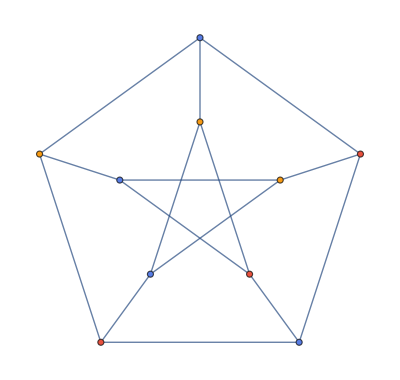

```mathematica
ColorGraphNodes[PetersenGraph[]]
```

Color the nodes of the Petersen graph with colors from color list 105:

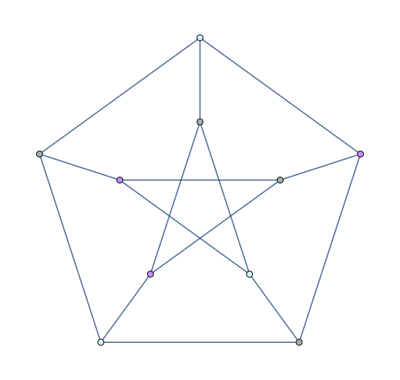

```mathematica
ColorGraphNodes[PetersenGraph[],ColorData["Atoms","ColorList"]]
```

Color the nodes with pastel colors.

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Author Name

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.